```mathematica
K={ 4.2, 0.4, 3.0 }
```

{4.2,0.4,3.}

```mathematica
U={{4.0/30.0,-2.0/3.0,22.0/30.0},{28.0/30.0,1.0/3.0,4.0/30.0},{-1.0/3.0,2.0/3.0,2.0/3.0}}
```

{{0.133333,-0.666667,0.733333},{0.933333,0.333333,0.133333},{-0.333333,0.666667,0.666667}}

```mathematica
extent={3,2,1}
```

{3,2,1}

```mathematica
V={-1.0,-1.0,-1.0}
```

{-1.,-1.,-1.}

```mathematica
phi=0.0
```

0.

```mathematica
cs=Cos[phi]
```

1.

```mathematica
sn=Sin[phi]
```

0.

```mathematica
tn=Tan[0.6]
```

0.684137

```mathematica
W0={0.0,0.832050264,-0.554700196}
```

{0.,0.83205,-0.5547}

```mathematica
W1={-0.963624120,0.148249879,0.222374782}
```

{-0.963624,0.14825,0.222375}

```mathematica
W2={0.267261267,0.534522533,0.801783800}
```

{0.267261,0.534523,0.801784}

```mathematica
hmin=0.5
```

0.5

```mathematica
hmax=3.0
```

3.

```mathematica
G0=-tn*cs*W0-tn*sn*W1+W2
```

{0.267261,-0.0347137,1.18127}

```mathematica
G1=tn*cs*W0+tn*sn*W1+W2
```

{0.267261,1.10376,0.422293}

```mathematica
J={{G0[[1]],G1[[1]]},{G0[[2]],G1[[2]]},{G0[[3]],G1[[3]]}}
```

{{0.267261,0.267261},{-0.0347137,1.10376},{1.18127,0.422293}}

```mathematica
F[x_]:=Dot[K+U.{x[[1]],x[[2]],x[[3]]}-V-J.{x[[4]],x[[5]]},K+U.{x[[1]],x[[2]],x[[3]]}-V-J.{x[[4]],x[[5]]}]/2
```

```mathematica
X={x0,x1,x2,x3,x4}
```

{x0,x1,x2,x3,x4}

```mathematica
F[X]
```

1/2 ((1.4+0.933333 x0+0.333333 x1+0.133333 x2+0.0347137 x3-1.10376 x4)^2+(4.-0.333333 x0+0.666667 x1+0.666667 x2-1.18127 x3-0.422293 x4)^2+(5.2+0.133333 x0-0.666667 x1+0.733333 x2-0.267261 x3-0.267261 x4)^2)

```mathematica
result=Minimize[{F[X],0.0≤x0≤2*extent[[1]]&&0.0≤x1≤2*extent[[2]]&&0.0≤x2≤2*extent[[3]]&&0≤x3&&0≤x4&&hmin≤x3+x4≤hmax},{x0,x1,x2,x3,x4}]
```

{8.32184,{x0→3.15384×10^-10,x1→2.05187,x2→8.41802×10^-11,x3→2.4089,x4→0.591098}}

```mathematica
distance=  Sqrt[2.0*result[[1]]]
```

4.07967

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTE\\Internal\\Development\\TestDistBoxCone\\SliceDistance.txt","CSV"]
```

{{-1.5708,0.185248},{-1.55334,0.208052},{-1.53589,0.23108},{-1.51844,0.254322},{-1.50098,0.277771},{-1.48353,0.301418},{-1.46608,0.325253},{-1.44862,0.34927},{-1.43117,0.373457},{-1.41372,0.397804},{-1.39626,0.422303},{-1.37881,0.446942},{-1.36136,0.47171},{-1.3439,0.496597},{-1.32645,0.521592},{-1.309,0.546683},{-1.29154,0.571859},{-1.27409,0.597107},{-1.25664,0.622416},{-1.23918,0.647773},{-1.22173,0.673167},{-1.20428,0.698584},{-1.18682,0.724014},{-1.16937,0.749441},{-1.15192,0.774855},{-1.13446,0.800242},{-1.11701,0.82559},{-1.09956,0.850887},{-1.0821,0.876119},{-1.06465,0.901274},{-1.0472,0.926086},{-1.02974,0.947485},{-1.01229,0.968596},{-0.994838,0.989411},{-0.977384,1.00993},{-0.959931,1.03013},{-0.942478,1.05002},{-0.925025,1.0696},{-0.907571,1.08884},{-0.890118,1.10776},{-0.872665,1.12634},{-0.855211,1.14457},{-0.837758,1.16246},{-0.820305,1.17999},{-0.802851,1.19716},{-0.785398,1.21397},{-0.767945,1.23041},{-0.750492,1.24647},{-0.733038,1.26216},{-0.715585,1.27746},{-0.698132,1.29237},{-0.680678,1.30688},{-0.663225,1.321},{-0.645772,1.33472},{-0.628319,1.34803},{-0.610865,1.36093},{-0.593412,1.37341},{-0.575959,1.38548},{-0.558505,1.39712},{-0.541052,1.40834},{-0.523599,1.41913},{-0.506145,1.42948},{-0.488692,1.43941},{-0.471239,1.44889},{-0.453786,1.45793},{-0.436332,1.46653},{-0.418879,1.47468},{-0.401426,1.48238},{-0.383972,1.48963},{-0.366519,1.49643},{-0.349066,1.50277},{-0.331613,1.50865},{-0.314159,1.51408},{-0.296706,1.51904},{-0.279253,1.52354},{-0.261799,1.52757},{-0.244346,1.53114},{-0.226893,1.53425},{-0.20944,1.53688},{-0.191986,1.53905},{-0.174533,1.54075},{-0.15708,1.54198},{-0.139626,1.54274},{-0.122173,1.54303},{-0.10472,1.54285},{-0.0872665,1.5422},{-0.0698132,1.54108},{-0.0523599,1.53949},{-0.0349066,1.53744},{-0.0174533,1.53491},{0,1.53192},{0.0174533,1.52846},{0.0349066,1.52453},{0.0523599,1.52014},{0.0698132,1.51529},{0.0872665,1.50997},{0.10472,1.5042},{0.122173,1.49796},{0.139626,1.49127},{0.15708,1.47528},{0.174533,1.45833},{0.191986,1.44123},{0.20944,1.42398},{0.226893,1.40658},{0.244346,1.38903},{0.261799,1.37134},{0.279253,1.35352},{0.296706,1.33556},{0.314159,1.31747},{0.331613,1.29925},{0.349066,1.28091},{0.366519,1.26245},{0.383972,1.24387},{0.401426,1.22519},{0.418879,1.2064},{0.436332,1.1875},{0.453786,1.1685},{0.471239,1.14941},{0.488692,1.13023},{0.506145,1.11096},{0.523599,1.09161},{0.541052,1.07217},{0.558505,1.05267},{0.575959,1.03309},{0.593412,1.01344},{0.610865,0.993732},{0.628319,0.973963},{0.645772,0.95414},{0.663225,0.934266},{0.680678,0.914344},{0.698132,0.894379},{0.715585,0.874375},{0.733038,0.854335},{0.750492,0.834264},{0.767945,0.814165},{0.785398,0.794042},{0.802851,0.773898},{0.820305,0.753738},{0.837758,0.733565},{0.855211,0.713383},{0.872665,0.693195},{0.890118,0.673004},{0.907571,0.652815},{0.925025,0.63263},{0.942478,0.610945},{0.959931,0.581204},{0.977384,0.55182},{0.994838,0.523222},{1.01229,0.495404},{1.02974,0.468346},{1.0472,0.442075},{1.06465,0.416612},{1.0821,0.391973},{1.09956,0.368167},{1.11701,0.345201},{1.13446,0.323078},{1.15192,0.301793},{1.16937,0.281344},{1.18682,0.261721},{1.20428,0.242915},{1.22173,0.224913},{1.23918,0.207702},{1.25664,0.191266},{1.27409,0.17559},{1.29154,0.160654},{1.309,0.146443},{1.32645,0.132937},{1.3439,0.120118},{1.36136,0.107967},{1.37881,0.0964655},{1.39626,0.0855952},{1.41372,0.0753371},{1.43117,0.0656737},{1.44862,0.0591183},{1.46608,0.0634971},{1.48353,0.0772861},{1.50098,0.0965277},{1.51844,0.118243},{1.53589,0.140336},{1.55334,0.162673},{1.5708,0.185248}}

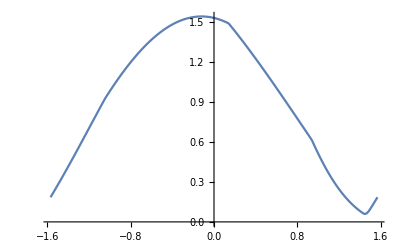

```mathematica
g=ListLinePlot[points]
```

```mathematica
vertline=Line[{{0,0},{0,1.65}}]
```

Line[{{0,0},{0,1.65}}]

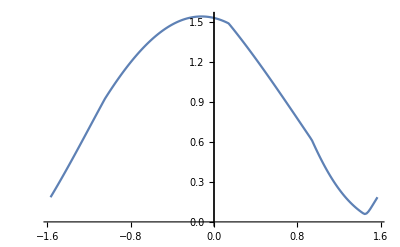

```mathematica
Show[g,Graphics[vertline]]
```

```mathematica
fn=(x-0.0625)*(x-2)*(x-3)+1
```

1+(-3+x) (-2+x) (-0.0625+x)

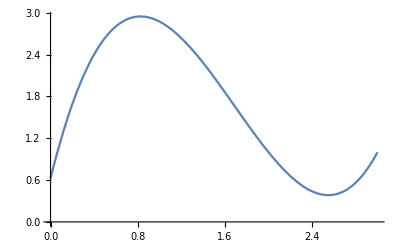

```mathematica
Plot[fn,{x,0,3}]
```

```mathematica
Minimize[{fn,0≤x&&x≤3},x]
```

{0.384344,{x→2.54976}}

```mathematica
fn=(x+0.0625)*(x-2)*(x-3)+1
```

1+(-3+x) (-2+x) (0.0625+x)

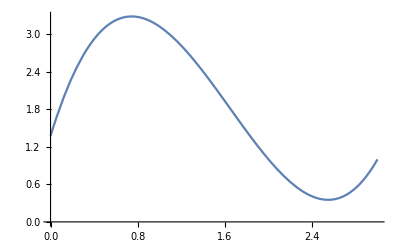

```mathematica
Plot[fn,{x,0,3}]
```

```mathematica
Minimize[{fn,0≤x&&x≤3},x]
```

{0.353389,{x→2.54746}}